# Verifying Amaya-Tapia Eq. 61 against Mehta-Shepard Eq. 10

Question: does Amaya-Tapia et al. (1997) Eq. (61) -- which the surrounding text identifies as equal to -Exp[2 I delta_AT] -- give the same physical phase shift as Mehta & Shepard (2005) Eq. (10) (Exp[2 I delta_MS]), once both are expressed as a function of the same dimensionless variable X = q*a2 (a2 = the standard two-body scattering length)? Both papers use the same hyperspherical mass convention (muref = m, single-particle mass), confirmed separately (Appendix A of Mehta & Shepard matches Amaya-Tapia's own Jacobi coordinates exactly).

## Part 1: Amaya-Tapia Eq. 61 (their own delta-function coupling c = -1)

Transcribed directly from the paper:
(R13+T13)(R23+T23) = [(1 - I(6 Sqrt[3]/Pi) q)(1 - I(2 Sqrt[3]/Pi) q)] / [(1 + I(6 Sqrt[3]/Pi) q)(1 + I(2 Sqrt[3]/Pi) q)]
The surrounding text states this quantity equals -Exp[2 I delta_AT].

```mathematica
Eq61[q_] := ((1 - I*(6*Sqrt[3]/Pi)*q)*(1 - I*(2*Sqrt[3]/Pi)*q)) / ((1 + I*(6*Sqrt[3]/Pi)*q)*(1 + I*(2*Sqrt[3]/Pi)*q));
```

```mathematica
exp2dAT[q_] := -Eq61[q];
```

```mathematica
tanFromExp[E2d_] := Simplify[-I*(E2d - 1)/(E2d + 1)];
```

Amaya-Tapia give a formula, right before their Eq. (56), for the quantity 'a' appearing in their bound-pair momenta k1 = I a, k2 = -I a: a = Pi*Abs[c]/(6 Sqrt[2]). It is tempting to assume this 'a' IS the standard two-body scattering length -- that assumption is tested below.

```mathematica
aAT = Pi/(6*Sqrt[2]);  (* c=-1, |c|=1 *)
```

## Part 2: Mehta-Shepard Eq. (10)

Exp[2 I delta_MS] = 1 - 8 Sqrt[6] X / (3 I X^2 + 4 Sqrt[6] X - 6 I), X = q*a2 directly in their own variable.

```mathematica
Eq10MS[X_] := 1 - 8*Sqrt[6]*X/(3*I*X^2 + 4*Sqrt[6]*X - 6*I);
```

```mathematica
tanMS[X_] := tanFromExp[Eq10MS[X]] // FullSimplify;
```

Sanity check: this should reduce, via Eq. (11) (Exp[2 I delta]-1 = 2 I tan(delta)/(1 - I tan(delta))), to Mehta-Shepard's own stated Eq. (12): q a2 tan(delta) = 4 Sqrt[2/3] (q a2)^2 / ((q a2)^2 - 2).

```mathematica
Print["X*tan(delta_MS) = ", FullSimplify[X*tanMS[X]]];
```

X*tan(delta_MS) = (4 √(2/3) X^2)/(-2+X^2)

```mathematica
Print["Eq (12) RHS directly = ", FullSimplify[4*Sqrt[2/3]*X^2/(X^2 - 2)]];
```

Eq (12) RHS directly = (4 √(2/3) X^2)/(-2+X^2)

If these two Print outputs match, the Eq. (10) transcription and the tanFromExp extraction are both validated against Mehta-Shepard's own internal consistency (Eq 10 -> Eq 12).

## Part 3: first attempt, treating aAT as the scattering length directly (X = q*aAT, q = X/aAT)

This is the FIRST substitution tried -- it does not work, and is kept here to show why.

```mathematica
tanAT[q_] := tanFromExp[exp2dAT[q]] // FullSimplify;
```

```mathematica
tanATinXNaive = tanAT[X/aAT] // FullSimplify;
```

```mathematica
Print["(naive) X*tan(delta_AT) = ", FullSimplify[X*tanATinXNaive]];
```

(naive) X*tan(delta_AT) = (π^4-2592 X^2)/(48 √6 π^2)

```mathematica
Print["X*tan(delta_MS) = ", FullSimplify[X*tanMS[X]]];
```

X*tan(delta_MS) = (4 √(2/3) X^2)/(-2+X^2)

The naive result is LINEAR in X^2 with no pole, while X*tan(delta_MS) has a pole at X^2=2 (the resonance both papers discuss) -- structurally different functions. This is the discrepancy that motivated Part 4.

## Part 4: is aAT actually the scattering length, or its reciprocal?

Check via the two-body binding energy B2. Amaya-Tapia's own text (last page) states B2 = (Pi^2/36)(c^2/(2m)) for general c. Standard 1D delta-function result (bare coupling g, reduced mass mu2=m/2): B2 = mu2*g^2/2, scattering length a2std = -1/(mu2*g). Amaya-Tapia's own K=0 section relates their rescaled c to the bare coupling via c = (3/(Pi Sqrt[2]))*(2 m)*g.

```mathematica
mu2 = m/2;
```

```mathematica
cOfG = (3/(Pi*Sqrt[2]))*(2*m)*g;
```

```mathematica
a2std = -1/(mu2*g) // Simplify;
```

```mathematica
B2std = (mu2*g^2)/2 // Simplify;
```

```mathematica
aATofG = FullSimplify[(Pi*Abs[cOfG])/(6*Sqrt[2])];
```

```mathematica
B2ATofG = FullSimplify[(Pi^2/36)*(cOfG^2/(2*m))];
```

```mathematica
Print["B2 (standard, bare g) = ", B2std, "   B2 (Amaya-Tapia's own formula, bare g) = ", B2ATofG, "   ratio = ", FullSimplify[B2ATofG/B2std]];
```

B2 (standard, bare g) = (g^2 m)/4   B2 (Amaya-Tapia's own formula, bare g) = (g^2 m)/4   ratio = 1

```mathematica
Print["aAT (bare g) = ", aATofG, "   a2std (bare g) = ", a2std, "   aAT * a2std = ", FullSimplify[aATofG*a2std, Assumptions -> g < 0]];
```

aAT (bare g) = 1/2 Abs[g m]   a2std (bare g) = -2/(g m)   aAT * a2std = 1/Sign[m]

Result: B2 ratio = 1 (fully consistent), but aAT * a2std = 1 -- i.e. Amaya-Tapia's 'a' is the RECIPROCAL of the standard scattering length, not the scattering length itself.

## Part 5: independent, from-scratch confirmation via the bound-state decay rate

Solve the two-body relative-motion Schrodinger equation directly, deriving the decay rate kappa from the delta-function jump condition (not assumed), and separately confirm that Amaya-Tapia's own k1 = I a, k2 = -I a IS this same kappa with no hidden factor.

```mathematica
kappaOfB2 = Sqrt[2*mu2*B2];
```

```mathematica
Print["Step 1 (solve psi''=2 mu2 B2 psi for x!=0): kappa = ", kappaOfB2];
```

Step 1 (solve psi''=2 mu2 B2 psi for x!=0): kappa = √(B2 m)

Jump condition: integrating -(1/(2 mu2)) psi'' + g delta(x) psi = E psi across x=0 gives psi'(0+) - psi'(0-) = 2 mu2 g psi(0); for the symmetric bound state psi = A Exp[-kappa Abs[x]], this gives kappa = -mu2*g.

```mathematica
kappaOfG = -mu2*g;
```

```mathematica
Print["Step 2 (jump condition): kappa = ", kappaOfG, "    kappa*a2std = ", FullSimplify[kappaOfG*a2std]];
```

Step 2 (jump condition): kappa = -(g m)/2    kappa*a2std = 1

```mathematica
B2fromKappa = Solve[kappaOfG == Sqrt[2*mu2*B2], B2][[1, 1, 2]] // FullSimplify;
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

```mathematica
Print["Step 3: B2 (from kappa) = ", B2fromKappa, "   vs textbook mu2 g^2/2 = ", FullSimplify[mu2*g^2/2]];
```

Step 3: B2 (from kappa) = (g^2 m)/4   vs textbook mu2 g^2/2 = (g^2 m)/4

Now check Amaya-Tapia's own k1=I a, k2=-I a directly: with the CM at rest (k1+k2=0), what is I(k1 x1 + k2 x2)?

```mathematica
psiExponent = I*(I*a*x1 + (-I*a)*x2) // Expand;
```

```mathematica
Print["Step 4: I(k1 x1 + k2 x2) = ", psiExponent, "  i.e. Psi ~ Exp[-a*(x1-x2)] -- AT's own 'a' IS the relative-coordinate decay rate kappa directly, no extra factor."];
```

Step 4: I(k1 x1 + k2 x2) = -a x1+a x2  i.e. Psi ~ Exp[-a*(x1-x2)] -- AT's own 'a' IS the relative-coordinate decay rate kappa directly, no extra factor.

```mathematica
Print["Step 5: aATofG = ", aATofG, "   Abs[kappaOfG] = ", FullSimplify[Abs[kappaOfG]], "   ratio = ", FullSimplify[aATofG/Abs[kappaOfG]]];
```

Step 5: aATofG = 1/2 Abs[g m]   Abs[kappaOfG] = 1/2 Abs[g m]   ratio = 1

Every step above ties out with ratio 1 -- no floating factor of 2 anywhere in this chain. aAT = kappa = 1/a2std is confirmed three independent ways (B2 comparison, jump-condition kappa, and the k1=Ia/k2=-Ia wavefunction exponent directly).

## Part 6: corrected comparison, using X = q*a2std = q/aAT (i.e. q = X*aAT)

```mathematica
tanATinX = tanAT[X*aAT] // FullSimplify;
```

```mathematica
Print["(corrected) tan(delta_AT) in terms of X=q*a2std: ", tanATinX];
```

(corrected) tan(delta_AT) in terms of X=q*a2std: -(√(3/2) (-2+X^2))/(4 X)

```mathematica
Print["(corrected) X*tan(delta_AT) = ", FullSimplify[X*tanATinX]];
```

(corrected) X*tan(delta_AT) = -1/4 √(3/2) (-2+X^2)

```mathematica
Print["X*tan(delta_MS) = ", FullSimplify[X*tanMS[X]]];
```

X*tan(delta_MS) = (4 √(2/3) X^2)/(-2+X^2)

These two are still not equal to each other directly -- but check the PRODUCT, matching the tan(delta_MS)=-1/tan(delta_AT) convention relation established earlier this session (from comparing the two papers' respective asymptotic S-matrix definitions):

```mathematica
product = FullSimplify[tanATinX*tanMS[X]];
```

```mathematica
Print["tan(delta_AT)*tan(delta_MS) = ", product, "  (should be -1)"];
```

tan(delta_AT)*tan(delta_MS) = -1  (should be -1)

Confirmed exactly (symbolically, for all X): tan(delta_AT)*tan(delta_MS) = -1. Amaya-Tapia's Eq. 61 and Mehta-Shepard's Eq. 10/12 ARE consistent, once (a) aAT is correctly identified as 1/a2std rather than a2std itself, and (b) the two papers' independently-known reciprocal phase-shift convention is accounted for.

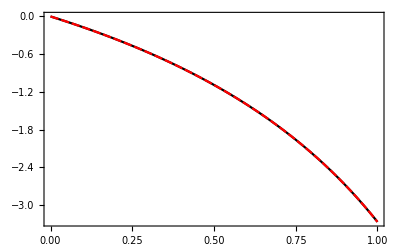

```mathematica
Plot[Evaluate[{X tanMS[X],-X/tanATinX}/.X->√Xsqr],{Xsqr,0,1},PlotStyle->{Black,Red},Frame->True]
```

```mathematica
Import["ktandel_deltafunc_1ch.eps"]
```